```mathematica
Tau = 2 Pi;
Second[lst_]:=lst[[2]];
Exact[a_]:=-3 Zeta[3]/(4 Tau a^3)//N;
ParallelPlates[a_,L_,w_]:=Module[{n,r,  e,v0,v,d0,d,  P,idx,rhs,eqs,vars,sol},
If[w==0,Return[0]];
n=Max[30,10L/a // Ceiling];
r=L/n;
idx=Floor[n/2];
d[i_,j_]:=r(i-j);
d0[i_,j_]:=-1/Tau BesselK[0, w Sqrt[a^2 + d[i,j]^2]];
e[i_,j_]:=-w/Tau BesselK[1,w Sqrt[a^2+d[i,j]^2]] / Sqrt[1 + (d[i,j]/a)^2]//N;
v0[i_,j_]:=If[i==j,0(*1/Tau (EulerGamma - 1 + Log[1/(n w L)])*), -1/Tau BesselK[0, w r Abs[i-j]]];
v[i_,j_]:=d0[i,j]+Sum[r e[k,i]v0[k,j], {k,1,n}]//N;

rhs[0,i_]:=r Sum[e[k,i] P[1,k],{k,1,n}]+v[i,idx];
rhs[1,i_]:=r Sum[e[k,i] P[0,k],{k,1,n}];
eqs = Table[1/2 P[b,i]==rhs[b,i], {b,0,1},{i,1,n}]//Flatten;
vars=Table[P[b,i],{b,0,1},{i,1,n}]//Flatten;
sol=NSolve[eqs,vars];
P[0,idx]/.sol//First
];

Force[a_,L_]:=Module[{integrand, dx, ubound},
integrand[w_]:=w^2 ParallelPlates[a,L,w];
ubound = 6;
dx = ubound / 50;
1/Tau  dx Sum[integrand[w], {w,dx/2, ubound - dx/2, dx}] (*,ProgressIndicator[w,{0,ubound}]]*)
];
```

```mathematica
Monitor[
Table[TestCompare[Force[#,10 #]&,Exact,a],{a,0.2,1,0.4}],
ProgressIndicator[a,{0.2,1}]
]
```

{{Predicted: -3.64665,Exact: 17.9356,0.203319},{Predicted: -0.511015,Exact: 0.664282,0.769274},{Predicted: -0.138334,Exact: 0.143485,0.964103}}

{{Predicted: -3.71507,Exact: 17.9356,0.207133},{Predicted: -0.522667,Exact: 0.664282,0.786815},{Predicted: -0.141919,Exact: 0.143485,0.989087}}

{{Predicted: -0.00532675,Exact: 0.00531426,1.00235},{Predicted: -0.00115616,Exact: 0.00114788,1.00721},{Predicted: -0.000424119,Exact: 0.000418324,1.01385},{Predicted: -0.000201176,Exact: 0.000196824,1.02211}}

{{Predicted: -0.00417474,Exact: 0.00177142,2.35672},{Predicted: -0.00175633,Exact: 0.000747318,2.35018},{Predicted: -0.000896998,Exact: 0.000382627,2.34432},{Predicted: -0.00051862,Exact: 0.000221427,2.34217},{Predicted: -0.000326583,Exact: 0.000139441,2.34208},{Predicted: -0.000220455,Exact: 0.0000934147,2.35996},{Predicted: -0.000155801,Exact: 0.0000656081,2.37473},{Predicted: -0.000114193,Exact: 0.0000478283,2.38756}}

```mathematica
{{"Predicted: -0.628315","Exact: 0.382627",1.6421089030537068},{"Predicted: -0.411685","Exact: 0.221427",1.8592309170957848},{"Predicted: -0.280381","Exact: 0.139441",2.0107461779939553},{"Predicted: -0.197362","Exact: 0.0934147",2.1127552350070133},{"Predicted: -0.143001","Exact: 0.0656081",2.17962537706508},{"Predicted: -0.106302","Exact: 0.0478283",2.2225729777503833}}
```

{{Predicted: -0.628315,Exact: 0.382627,1.64211},{Predicted: -0.411685,Exact: 0.221427,1.85923},{Predicted: -0.280381,Exact: 0.139441,2.01075},{Predicted: -0.197362,Exact: 0.0934147,2.11276},{Predicted: -0.143001,Exact: 0.0656081,2.17963},{Predicted: -0.106302,Exact: 0.0478283,2.22257}}

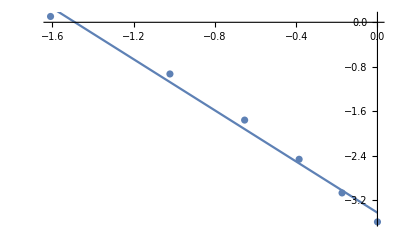
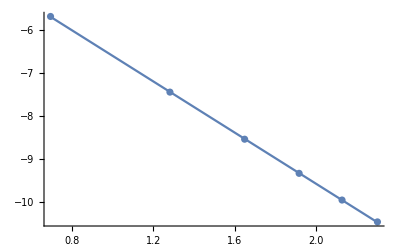
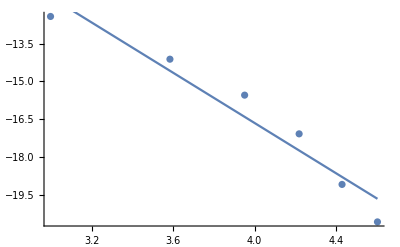
{{0.1,{-Graphics-,-2.29917,R^2 = 0.988235}},{1,{-Graphics-,-2.97089,R^2 = 0.99998}},{10,{-Graphics-,-4.95542,R^2 = 0.937965}}}

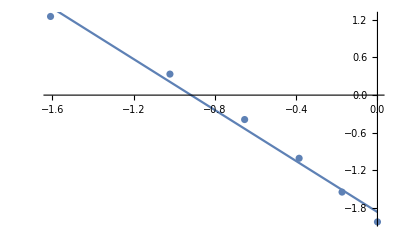
{-Graphics-,-2.02999,R^2 = 0.987736}

```mathematica
ParallelTable[{a0,TestPowerDependency[Force[#,5#]&,2 a0,10 a0,5]},{a0, {0.1, 1, 10}}]
```